## Load packages and global definitions

```mathematica
SetDirectory[NotebookDirectory[]];
Get["../../Mathematica_packages/QMB.wl"]
Get["../../Mathematica_packages/Chaometer.wl"]
```

## Calculos

```mathematica
L=9;(* number of spins *)
{J,hx,hz}={1,1,0.5};
```

Compute eigenvalues and eigenvectors of Hamiltonian:

```mathematica
{eigenvalsH,eigenvecsH}=Transpose[Sort[Transpose[Chop[Eigensystem[IsingNNOpenHamiltonian[hx,hz,J,L]]]]]];
```

```mathematica
SeedRandom[20349];
ψE=RandomChainProductState[L-1];
```

```mathematica
t=Power[10,Range[-2,2,0.05]];
```

```mathematica
AbsoluteTiming[superoperators=Chop[Superoperator[#,ψE,eigenvalsH,eigenvecsH,L]]&/@t;]
```

{44.9982,Null}

```mathematica
chois=1/2*Reshuffle/@superoperators;
```

```mathematica
choiPurities=Chop[Purity/@chois];
```

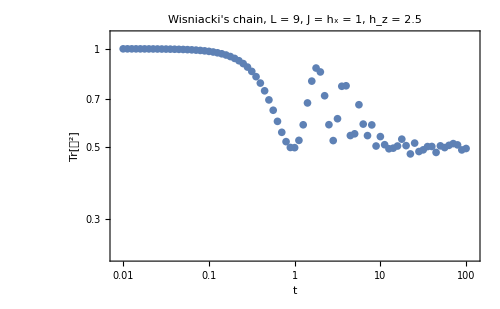

```mathematica
ListLogLogPlot[Transpose[{t,choiPurities}],
PlotRange->{{0.01-0.0015,120},{0.24-0.01,1+0.1}},
Frame->True,
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
FrameStyle->Directive[Black,FontSize->21],
FrameTicks->{{myTicksYLeft,myTicksYRight},{myTicksXBelow,myTicksXAbove}},
FrameTicksStyle->Directive[Black,19],
GridLines->{Table[10^i,{i,-2,2}],Range[0.25,1,0.05]},
ImageSize->500,
PlotLabel->"Wisniacki's chain, "<>ToString[TraditionalForm[HoldForm[L]]]<>" = "<>ToString[L]<>", J = h_x = 1, h_z = 2.5",
LabelStyle->Directive[Black,FontSize->17]
]
```

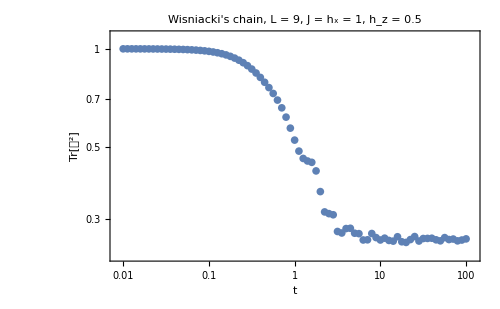

```mathematica
ListLogLogPlot[Transpose[{t,choiPurities}],
PlotRange->{{0.01-0.0015,120},{0.24-0.01,1+0.1}},
Frame->True,
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
FrameStyle->Directive[Black,FontSize->21],
FrameTicks->{{myTicksYLeft,myTicksYRight},{myTicksXBelow,myTicksXAbove}},
FrameTicksStyle->Directive[Black,19],
GridLines->{Table[10^i,{i,-2,2}],Range[0.25,1,0.05]},
ImageSize->500,
PlotLabel->"Wisniacki's chain, "<>ToString[TraditionalForm[HoldForm[L]]]<>" = "<>ToString[L]<>", J = h_x = 1, h_z = 0.5",
LabelStyle->Directive[Black,FontSize->17]
]
```